```mathematica
Subscript[A, L] = 2*u*(Subscript[k, L]+1)*(Subscript[k, L]+2)/(Subscript[k, L]^2+3*Subscript[k, L]*(1-δ^2)+2*(1-δ^2));
```

```mathematica
Subscript[A, l] = Subscript[A, L]/.{Subscript[k, L]-> Subscript[k, l]};
```

```mathematica
Subscript[B, L] = T^4*u^3*(Subscript[k, l]^4+7*Subscript[k, l]^3*(1-δ^2)+6*Subscript[k, l]^2*(3-5*δ^2+2*δ^4)+20*Subscript[k, l]*(1-δ^2)^2+8*(1-δ^2)^2)/(2+Subscript[k, l]^2);
```

```mathematica
Subscript[B, l] = Subscript[B, L]/.{Subscript[k, l]->Subscript[k, L]}
```

(T^4 u^3 (8 (1-δ^2)^2+20 (1-δ^2)^2 k_L+6 (3-5 δ^2+2 δ^4) k_L^2+7 (1-δ^2) k_L^3+k_L^4))/(2+k_L^2)

```mathematica
Subscript[C, L] = -T^3*u^3*(2+Subscript[k, L])*(Subscript[k, l]^2+3 Subscript[k, l]*(1-δ^2)+2*(1-δ^2));
```

```mathematica
Subscript[c, mid]=Subscript[C, L]/.{Subscript[k, l]-> a,Subscript[k, L]-> Subscript[k, l]}
```

-T^3 u^3 (a^2+2 (1-δ^2)+3 a (1-δ^2)) (2+k_l)

```mathematica
Subscript[C, l] = Subscript[c, mid]/.{a-> Subscript[k, L]}
```

-T^3 u^3 (2+k_l) (2 (1-δ^2)+3 (1-δ^2) k_L+k_L^2)

```mathematica
Subscript[D, L] = Subscript[B, L]*(Subscript[k, L]^2+4*Subscript[k, L]*(1-δ^2)+4*(1-δ^2))/(Subscript[k, L]+1)
```

(T^4 u^3 (8 (1-δ^2)^2+20 (1-δ^2)^2 k_l+6 (3-5 δ^2+2 δ^4) k_l^2+7 (1-δ^2) k_l^3+k_l^4) (4 (1-δ^2)+4 (1-δ^2) k_L+k_L^2))/((2+k_l^2) (1+k_L))

```mathematica
Subscript[D, l] = Subscript[B, l]*(Subscript[k, l]^2+4*Subscript[k, l]*(1-δ^2)+4*(1-δ^2))/(Subscript[k, l]+1)
```

(T^4 u^3 (4 (1-δ^2)+4 (1-δ^2) k_l+k_l^2) (8 (1-δ^2)^2+20 (1-δ^2)^2 k_L+6 (3-5 δ^2+2 δ^4) k_L^2+7 (1-δ^2) k_L^3+k_L^4))/((1+k_l) (2+k_L^2))

```mathematica
J =-2*δ*κ/(π*γ)*(Subscript[d, l]*Exp[-Subscript[A, l]]*Sqrt[Subscript[B, l]]/Subscript[C, l]-Subscript[d, L]*Exp[-Subscript[A, L]]*Sqrt[Subscript[B, L]]/Subscript[C, L])/(Subscript[d, l]*Erf[Subscript[A, l]]*Sqrt[Subscript[D, l]]/Subscript[C, l]+Subscript[d, L]*Erf[Subscript[A, L]]*Sqrt[Subscript[D, L]]/Subscript[C, L])
```

-(2 δ κ ((ⅇ^(-(2 u (1+k_L) (2+k_L))/(2 (1-δ^2)+3 (1-δ^2) k_L+k_L^2)) d_L √((T^4 u^3 (8 (1-δ^2)^2+20 (1-δ^2)^2 k_l+6 (3-5 δ^2+2 δ^4) k_l^2+7 (1-δ^2) k_l^3+k_l^4))/(2+k_l^2)))/(T^3 u^3 (2 (1-δ^2)+3 (1-δ^2) k_l+k_l^2) (2+k_L))-(ⅇ^(-(2 u (1+k_l) (2+k_l))/(2 (1-δ^2)+3 (1-δ^2) k_l+k_l^2)) d_l √((T^4 u^3 (8 (1-δ^2)^2+20 (1-δ^2)^2 k_L+6 (3-5 δ^2+2 δ^4) k_L^2+7 (1-δ^2) k_L^3+k_L^4))/(2+k_L^2)))/(T^3 u^3 (2+k_l) (2 (1-δ^2)+3 (1-δ^2) k_L+k_L^2))))/(π γ (-(Erf[(2 u (1+k_L) (2+k_L))/(2 (1-δ^2)+3 (1-δ^2) k_L+k_L^2)] d_L √((T^4 u^3 (8 (1-δ^2)^2+20 (1-δ^2)^2 k_l+6 (3-5 δ^2+2 δ^4) k_l^2+7 (1-δ^2) k_l^3+k_l^4) (4 (1-δ^2)+4 (1-δ^2) k_L+k_L^2))/((2+k_l^2) (1+k_L))))/(T^3 u^3 (2 (1-δ^2)+3 (1-δ^2) k_l+k_l^2) (2+k_L))-(Erf[(2 u (1+k_l) (2+k_l))/(2 (1-δ^2)+3 (1-δ^2) k_l+k_l^2)] d_l √((T^4 u^3 (4 (1-δ^2)+4 (1-δ^2) k_l+k_l^2) (8 (1-δ^2)^2+20 (1-δ^2)^2 k_L+6 (3-5 δ^2+2 δ^4) k_L^2+7 (1-δ^2) k_L^3+k_L^4))/((1+k_l) (2+k_L^2))))/(T^3 u^3 (2+k_l) (2 (1-δ^2)+3 (1-δ^2) k_L+k_L^2))))

```mathematica
Subscript[J, fin] = J/.{Subscript[k, l]-> k/(1+λ^(-1))^2,Subscript[k, L]-> k/(1+λ)^2}
```

-((2 δ κ (-((ⅇ^(-(2 u (1+k/(1+1/λ)^2) (2+k/(1+1/λ)^2))/(2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2)) √((T^4 u^3 (8 (1-δ^2)^2+k^4/(1+λ)^8+(7 k^3 (1-δ^2))/(1+λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+λ)^4+(20 k (1-δ^2)^2)/(1+λ)^2))/(2+k^2/(1+λ)^4)) d_l)/(T^3 u^3 (2+k/(1+1/λ)^2) (2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)))+(ⅇ^(-(2 u (1+k/(1+λ)^2) (2+k/(1+λ)^2))/(2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)) √((T^4 u^3 (8 (1-δ^2)^2+k^4/(1+1/λ)^8+(7 k^3 (1-δ^2))/(1+1/λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+1/λ)^4+(20 k (1-δ^2)^2)/(1+1/λ)^2))/(2+k^2/(1+1/λ)^4)) d_L)/(T^3 u^3 (2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2) (2+k/(1+λ)^2))))/(π γ (-((√((T^4 u^3 (4 (1-δ^2)+k^2/(1+1/λ)^4+(4 k (1-δ^2))/(1+1/λ)^2) (8 (1-δ^2)^2+k^4/(1+λ)^8+(7 k^3 (1-δ^2))/(1+λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+λ)^4+(20 k (1-δ^2)^2)/(1+λ)^2))/((1+k/(1+1/λ)^2) (2+k^2/(1+λ)^4))) Erf[(2 u (1+k/(1+1/λ)^2) (2+k/(1+1/λ)^2))/(2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2)] d_l)/(T^3 u^3 (2+k/(1+1/λ)^2) (2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)))-(√((T^4 u^3 (8 (1-δ^2)^2+k^4/(1+1/λ)^8+(7 k^3 (1-δ^2))/(1+1/λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+1/λ)^4+(20 k (1-δ^2)^2)/(1+1/λ)^2) (4 (1-δ^2)+k^2/(1+λ)^4+(4 k (1-δ^2))/(1+λ)^2))/((2+k^2/(1+1/λ)^4) (1+k/(1+λ)^2))) Erf[(2 u (1+k/(1+λ)^2) (2+k/(1+λ)^2))/(2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)] d_L)/(T^3 u^3 (2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2) (2+k/(1+λ)^2)))))

```mathematica
Subscript[J, simp] = Simplify[π*γ/κ*Subscript[J, fin]/.{λ->1/9,k-> 1,u->1,Subscript[d, l]-> 1,Subscript[d, L]-> 9,T-> 1}]
```

(365620 ⅇ^((4 (-1032529161+965906300 δ^2))/((-20301+20300 δ^2) (-50861+44300 δ^2))) δ (16016283 √20001 ⅇ^(40602/(20301-20300 δ^2)) (-50861+44300 δ^2) √(820180701-1640300700 δ^2+820120000 δ^4)-1873427 √26561 ⅇ^(101722/(50861-44300 δ^2)) (-20301+20300 δ^2) √(4016035421-7180308700 δ^2+3207320000 δ^4)))/(1617644583 √3620181 (-50861+44300 δ^2) √(64762288331661-188900866325100 δ^2+183515266000000 δ^4-59376688000000 δ^6) Erf[101722/(50861-44300 δ^2)]+339090287 √2682661 (-20301+20300 δ^2) √(162251847043821-452339482797100 δ^2+419663406800000 δ^4-129575728000000 δ^6) Erf[40602/(20301-20300 δ^2)])

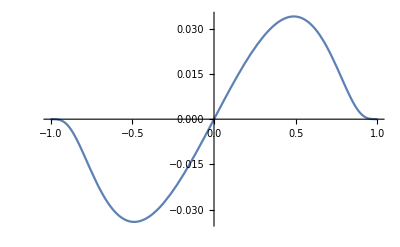

```mathematica
Plot[%13,{δ,-1,1}]
```

```mathematica
Subscript[J, fin]
```

-((2 δ κ (-((ⅇ^(-(2 u (1+k/(1+1/λ)^2) (2+k/(1+1/λ)^2))/(2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2)) √((T^4 u^3 (8 (1-δ^2)^2+k^4/(1+λ)^8+(7 k^3 (1-δ^2))/(1+λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+λ)^4+(20 k (1-δ^2)^2)/(1+λ)^2))/(2+k^2/(1+λ)^4)) d_l)/(T^3 u^3 (2+k/(1+1/λ)^2) (2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)))+(ⅇ^(-(2 u (1+k/(1+λ)^2) (2+k/(1+λ)^2))/(2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)) √((T^4 u^3 (8 (1-δ^2)^2+k^4/(1+1/λ)^8+(7 k^3 (1-δ^2))/(1+1/λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+1/λ)^4+(20 k (1-δ^2)^2)/(1+1/λ)^2))/(2+k^2/(1+1/λ)^4)) d_L)/(T^3 u^3 (2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2) (2+k/(1+λ)^2))))/(π γ (-((√((T^4 u^3 (4 (1-δ^2)+k^2/(1+1/λ)^4+(4 k (1-δ^2))/(1+1/λ)^2) (8 (1-δ^2)^2+k^4/(1+λ)^8+(7 k^3 (1-δ^2))/(1+λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+λ)^4+(20 k (1-δ^2)^2)/(1+λ)^2))/((1+k/(1+1/λ)^2) (2+k^2/(1+λ)^4))) Erf[(2 u (1+k/(1+1/λ)^2) (2+k/(1+1/λ)^2))/(2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2)] d_l)/(T^3 u^3 (2+k/(1+1/λ)^2) (2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)))-(√((T^4 u^3 (8 (1-δ^2)^2+k^4/(1+1/λ)^8+(7 k^3 (1-δ^2))/(1+1/λ)^6+(6 k^2 (3-5 δ^2+2 δ^4))/(1+1/λ)^4+(20 k (1-δ^2)^2)/(1+1/λ)^2) (4 (1-δ^2)+k^2/(1+λ)^4+(4 k (1-δ^2))/(1+λ)^2))/((2+k^2/(1+1/λ)^4) (1+k/(1+λ)^2))) Erf[(2 u (1+k/(1+λ)^2) (2+k/(1+λ)^2))/(2 (1-δ^2)+k^2/(1+λ)^4+(3 k (1-δ^2))/(1+λ)^2)] d_L)/(T^3 u^3 (2 (1-δ^2)+k^2/(1+1/λ)^4+(3 k (1-δ^2))/(1+1/λ)^2) (2+k/(1+λ)^2)))))

```mathematica
Subscript[J, simp] = Simplify[π*γ/κ*Subscript[J, fin]/.{λ->1/9,k-> 1,u->1,Subscript[d, l]-> 1,Subscript[d, L]-> 9},Assumptions->{T>0}]
```

(365620 ⅇ^((4 (-1032529161+965906300 δ^2))/((-20301+20300 δ^2) (-50861+44300 δ^2))) δ (16016283 √20001 ⅇ^(40602/(20301-20300 δ^2)) (-50861+44300 δ^2) √(820180701-1640300700 δ^2+820120000 δ^4)-1873427 √26561 ⅇ^(101722/(50861-44300 δ^2)) (-20301+20300 δ^2) √(4016035421-7180308700 δ^2+3207320000 δ^4)))/(1617644583 √3620181 (-50861+44300 δ^2) √(64762288331661-188900866325100 δ^2+183515266000000 δ^4-59376688000000 δ^6) Erf[101722/(50861-44300 δ^2)]+339090287 √2682661 (-20301+20300 δ^2) √(162251847043821-452339482797100 δ^2+419663406800000 δ^4-129575728000000 δ^6) Erf[40602/(20301-20300 δ^2)])

```mathematica
Plot[%32,{δ,-1,1}]
```

-Graphics-

```mathematica
Subscript[J, michael] = k*δ/(2*π*γ)*Exp[-2*u]/((1+λ)*Erf[Sqrt[2*u]])*(λ*Sqrt[(1+k*λ^2/(1+λ)^2)/((2+k*λ^2/(1+λ)^2)^2+δ^2*(1+k*λ^2/(1+λ)^2))]-Sqrt[(1+k/(1+λ)^2)/((2+k/(1+λ)^2)^2+δ^2*(1+k/(1+λ)^2))]);
```

```mathematica
Subscript[J, micsim] = Simplify[π*γ*Subscript[J, michael]/.{λ->9,k-> 1,u->1,Subscript[d, l]-> 1,Subscript[d, L]-> 9},Assumptions->{T>0}]
```

-(δ (√101 √(1/(40401+10100 δ^2))-9 √181 √(1/(78961+18100 δ^2))))/(2 ⅇ^2 Erf[√2])

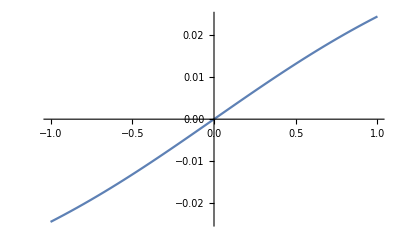

```mathematica
Plot[%55,{δ,-1,1}]
```